### Two Trader Equilibrium in the OW Model - Exact Solution

#### Define trading and cost functions cost functions

```mathematica
(*Input variables*)
as=0.1; (*Example value*)
ae=0.1; (*Example value*)
an = {0.2,0.1,-0.3};
bs=0.2; (*Example value*)
be=0.3; (*Example value*)
bn = {0, -0.3, 0.25};
rho=10; (*Example value*)
lambda=2; (*Example value*)

(* Auxilliary variables*)
mua = 1 - as-ae;
mub = 1 - bs - be;
```

### Trading Schedules

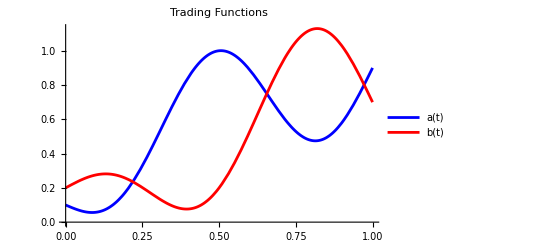

```mathematica
a[t_,as_,ae_,ai_]:=Piecewise[{
{0,t==0},
{as+(1-as-ae) t+Sum[ai[[i]] Sin[i π t],{i,1,Length[ai]}],0<t<1},
{1,t==1}}
]

b[t_,bs_,be_,bi_]:=Piecewise[{
{0,t==0},
{bs+(1-bs-be) t+Sum[bi[[i]] Sin[i π t],{i,1,Length[bi]}],0<t<1},
{1,t==1}}]

Plot[
{a[t,as,ae,an],b[t,bs, be, bn]},{t,0,1},
PlotStyle->{Blue,Red}, PlotLegends->{"a(t)","b(t)"},
PlotLabel->"Trading Functions"
]
```

### Price Impact